```mathematica
ME314 Final Project;
FeiyuChen;
This is the __main__ file of my project;
```

```mathematica
(*Quit[]*)
(*Open and run all other Mathematica scripts*)
(*myOpenFile[filename_]:=Module[{nb1},nb1=NotebookOpen[NotebookDirectory[]<>"/"<>filename];
     SelectionMove[nb1,All,Notebook];
     SelectionEvaluate[nb1]
]
myOpenFile["funcs_math.nb"];
myOpenFile["funcs_assist.nb"];
myOpenFile["funcs_main.nb"];*)
```

```mathematica
(*Put your code here to create links system*)
CreateObjects:=Module[{},

(* ------ Output of createLink ------
The link class returned by createLink has 5 elements;
{T,pFront,pBack,TFront,TBack};

If you want to use them to add constraint or extend more links,You can access them by index:
IdxT=1;IdxPFront=2;IdxPBack=3;IdxTFront=4;IdxTBack=5;
Such as:
link1=createLink3DOFpp[p0,p1]
link1[[IdxTFront]]
*)

(* Example 1: Polygon with NumOfEdges *)
nthGroup=1;
initRandVelocity=3;

p0={-1,0};
p1={-0.5,0.2};
l=CalcDistpp[p0,p1];

NumOfEdges=5;
linki=createLink3DOFpp[p0,p1];
For[i=1,i≤NumOfEdges,i=i+1,
linki=createLink0DOFgθl[linki[[IdxTFront]],2*Pi/NumOfEdges,l]
];

(* Example 2: 2-links*)
nthGroup=2;
initRandVelocity=1.0;

gFix=Trans4[0,1];
createVertex[gFix];
link4=createLink1DOFgθl[gFix,0,1.2];
link5=createLink1DOFgθl[link4[[IdxTFront]],-3*Pi/4,1.5];

(* Example 3: 1-link with constrainted height*)

nthGroup=3;
initRandVelocity=0;

p0={-1.8,1.8};
p1={-1.2,1.8};

link6=createLink3DOFpp[p0,p1];
addConstraint[link6[[IdxPBack]][[2]]==0];

(* Example 3: A square wall with 4 edges *);
nthGroup=10;
pWalls={{-2,+2.2},{+2.2,+2},{+2,-2.2},{-2.2,-2}};
AppendTo[pWalls,pWalls[[1]]];
For[i=1,i≤4,i++,
createLink0DOFpp[pWalls[[i]],pWalls[[i+1]]]
];

(* Example 4: A wall in the middle *)
createLink0DOFpp[{1,-1.2},{1.5,-0.6}];

];
```

```mathematica
(* Set up all things *)
mainResetVars;
CreateObjects;
RemoveDuplicateVertexs;

Print["Start Solving ..."];
mainSolveELeqs;
Print["Finish Solving ..."];

Print["Start setting impact ..."];
SetUpImpacts[];
Print["Finish setting impact ..."];
```

Start Solving ...

Finish Solving ...

Start setting impact ...

Finish setting impact ...

LessEqual::nord: Invalid comparison with 4.37132-1.89527×10^-16 ⅈ attempted.

LessEqual::nord: Invalid comparison with 4.37129-1.89535×10^-16 ⅈ attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

Computing simulation is completed.

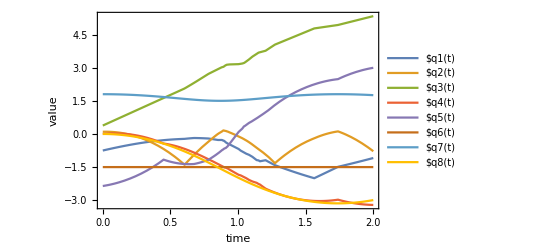

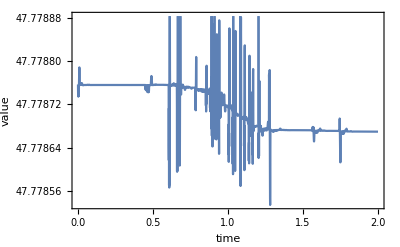

```mathematica
(* Set up params for NDSolve *)
timeend=2;(* total simulation time *)
MAXIMPACTTIMES=1000;
impactDetectionError=0.1;
intergrationMaxStepSize=0.01;
ifprint=False;

ddqSolve=TurnToEq[ddqs,EQ[[1,;;,2]]];

(* NDsolve and Play simulation *)
{end,data,bounces}=mainNDSolveSimulation[qsInit,dqsInit];

(* Plot *)

plotVariablesValues
plotHamValues
plotAnimation
```